### Using image processing well-studied fitness functions

### Finding a fitness function that produces complex behavior from random initial conditions

#### Challenges

Fitness functions for some static density tend to lead to simple attractor rules

Sin curve is too specific a state to make progress towards and leads to rules getting stuck in bad local minima

The goal is to get bulk orchestration, really you’d like to have a metric for 2D density, sin is like this but doesn’t quite work, what should I use instead?

I’m imagining now some renormalization type thing. I mean the characteristic

I mean the fundamental thing we want to happen is to have some bulk structure emerge. But the sine wave for this system is almost too bulk,

#### What about going for a checkerboard pattern? I think that’s a decent idea.

```mathematica
Module[{s = 5, width = 200, length  = 120}, ArrayPlot[Table[Mod[Quotient[i,s]+Quotient[j,s],2],{i,length},{j,width}],ColorRules->{0->White,1->Black},Frame->False, Mesh->True, MeshStyle->Opacity[.1]]]
```

-Graphics-

```mathematica
evo  = Module[
{deep = 6000,initru, nru, nfit, inits, cboard},
SeedRandom[3433113];
initru = {ResourceFunction["RandomCA"][{2, 2},"Quiescent"->True]["RuleNumber"], 2, 2};
cboard = Table[Mod[Quotient[i,5]+Quotient[j,5],2],{i,120},{j,200}];
NestList[Function[{ru, fitness}, 
nru={{"[◼]", "RandomRuleMutation"}}[ru];
nfit =Total[Abs[cboard - CellularAutomaton[nru, RandomInteger[1, 200], 119]], 2];
If[nfit<=fitness, {nru, nfit}, {ru, fitness}]]@@#&,{initru,Infinity},deep]];
```

```mathematica
ArrayPlot[CellularAutomaton[#,inits, 120]]&/@ GatherBy[evo, Last][[All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

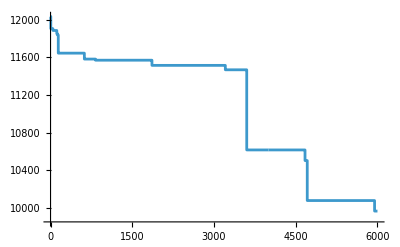

```mathematica
ListStepPlot[evo[[All, -1]]]
```

```mathematica
Differences[]
```

### Using high variation in densities

```mathematica
evo  = Module[
{deep = 4000,initru, nru, nfit, inits, cboard},
SeedRandom[3433116];
initru = {ResourceFunction["RandomCA"][{2, 2},"Quiescent"->True]["RuleNumber"], 2, 2};
NestList[Function[{ru, fitness}, 
nru={{"[◼]", "RandomRuleMutation"}}[ru];
nfit =Total[Differences[
(Total[CellularAutomaton[nru, RandomInteger[1, 200], 119]]/200), 2, 10]];
If[nfit>=fitness, {nru, nfit}, {ru, fitness}]]@@#&,{initru,-Infinity},deep]];
```

```mathematica
ArrayPlot[CellularAutomaton[#,RandomInteger[1, 200], 120]]&/@ GatherBy[evo, Last][[All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

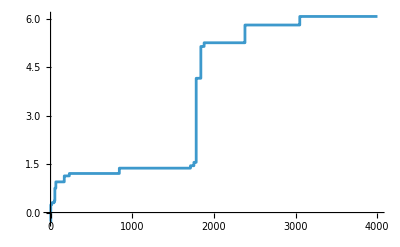

```mathematica
ListStepPlot[evo[[All, -1]]]
```

### Trying with exhausitve search

```mathematica
Module[{s = 10, width = 200, length  = 120}, ArrayPlot[Table[Mod[Quotient[i,s]+Quotient[j,s],2],{i,length},{j,width}],ColorRules->{0->White,1->Black},Frame->False, Mesh->True, MeshStyle->Opacity[.1]]]
```

-Graphics-

```mathematica
out = Module[{s = 10, width = 200, length  = 120, cboard},
SeedRandom[111111];
cboard = Table[Mod[Quotient[i,s]+Quotient[j,s],2],{i,length},{j,width}];SortBy[Table[ResourceFunction["RandomCA"][{2, 2}, "Quiescent"->True], 10000], 
Total[Abs[cboard - CellularAutomaton[#, RandomInteger[1, width], length - 1]], 2]&, 10]];
```

```mathematica
Module[{s = 10, width = 200, length  = 120, cboard},ArrayPlot[CellularAutomaton[{#RuleNumber, 2, 2}, RandomInteger[1, width], length - 1]]&/@out[[;;10]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Looking at cumalative for many more steps

```mathematica
rudiffs = Module[{width = 200, length  = 500},
SeedRandom[222222];
Append[#,"d2/10"->Total[Abs[Differences[Total[CellularAutomaton[#, RandomInteger[1, width], {{200, length +200- 1 }} - 1]], 1, 10]]]]&/@ Table[ResourceFunction["RandomCA"][{2, 2}, "Quiescent"->True], 1000]];
```

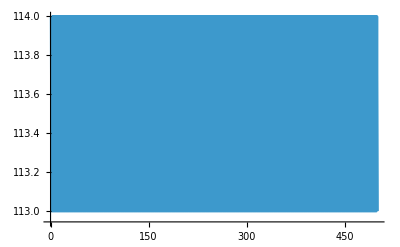
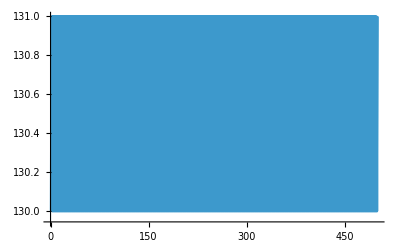
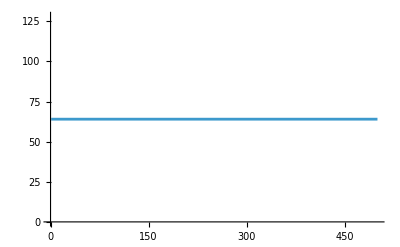
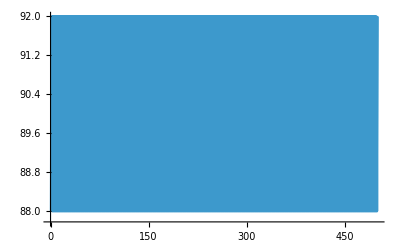
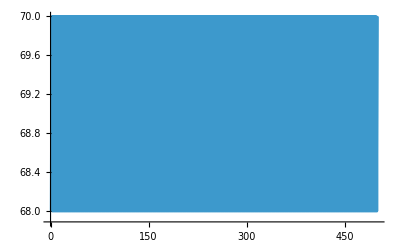
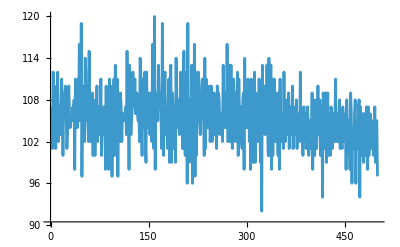
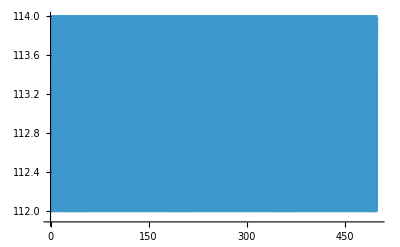
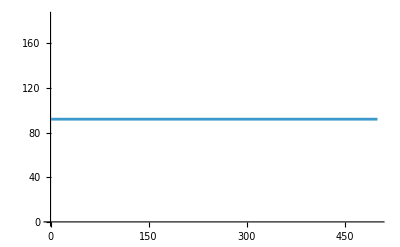

```mathematica
Module[{width = 200, length  = 500},ListLinePlot[Total/@ (CellularAutomaton[{#RuleNumber, 2, 2}, RandomInteger[1, width],{{200, length +200- 1 }}]&)@#, PlotRange->All]]&/@ ReverseSortBy[rudiffs, #["d2/10"]&][[;;10]]
```

```mathematica
Module[{width = 200, length  = 500},Labeled[ArrayPlot[CellularAutomaton[{#RuleNumber, 2, 2}, RandomInteger[1, width], {{120, length +120- 1 }}]], Text[#["d2/10"]]]&/@ReverseSortBy[rudiffs, #["d2/10"]&][[;;10]]]
```

{-Graphics-67500,-Graphics-67000,-Graphics-59000,-Graphics-56500,-Graphics-52500,-Graphics-52394,-Graphics-51338,-Graphics-50000,-Graphics-48967,-Graphics-48666}

#### Taking the mean every ten steps and then summing the total variation

```mathematica
Mean[{{0, 1}, {3, 3}}]
```

{3/2,2}

```mathematica
rudiffs = Module[{width = 200, length  = 500, chunksize},
SeedRandom[222222];
Append[#,"diffmean"->Total[Abs[Differences[Total[CellularAutomaton[#, RandomInteger[1, width], {{200, length +200- 1 }} - 1]], 1, 10]]]]&/@ Table[ResourceFunction["RandomCA"][{2, 2}, "Quiescent"->True], 1000]];
```

### Looking my damn self

```mathematica
Module[{s = 10, width = 200, length  = 120, cboard},ArrayPlot[CellularAutomaton[{#RuleNumber, 2, 2}, RandomInteger[1, width], length - 1]]&/@Table[ResourceFunction["RandomCA"][{2, 2}, "Quiescent"->True], 30]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Measuring macroscopic features of known class-4 rules

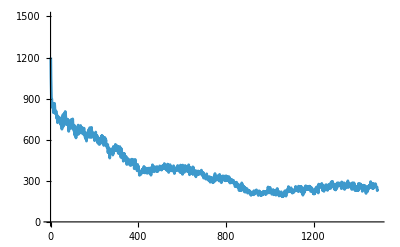

```mathematica
ListLinePlot[Total/@CellularAutomaton[{1815,{3,1}},RandomInteger[2,1200],1490], PlotRange->1500]
```

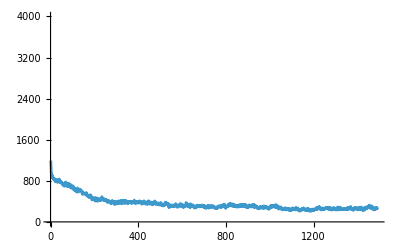
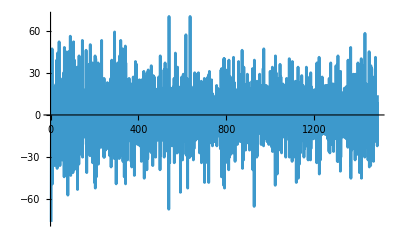
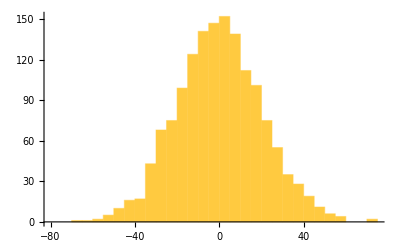
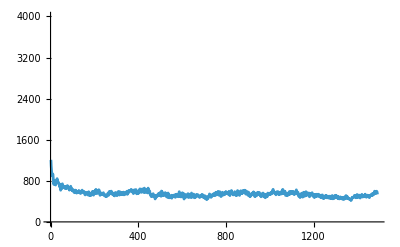
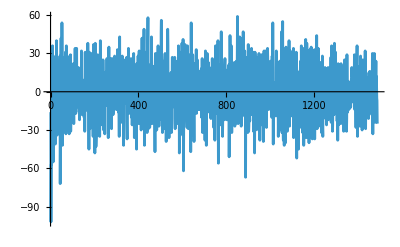
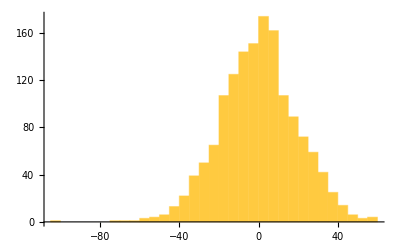
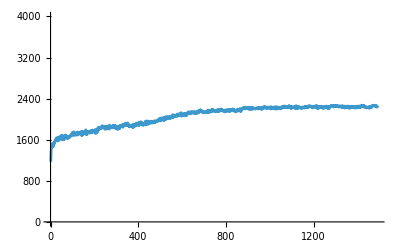
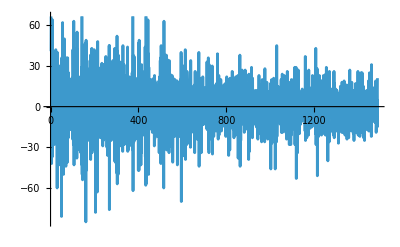
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
{ListLinePlot[Total/@#, PlotHighlighting->None, PlotRange->4000],ListLinePlot[Differences[Total/@ #], PlotHighlighting->None],Histogram[Differences[Total/@ #]],Rasterize[ArrayPlot[#]]}&[CellularAutomaton[{#,{3,1}},RandomInteger[2,1200],1490]]&/@ {1815, 2007, 1659, 2043}
```

#### Random for comp

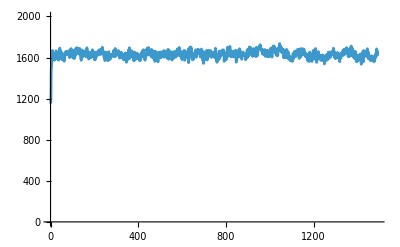
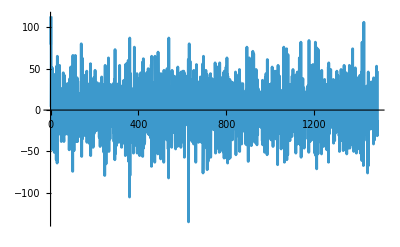
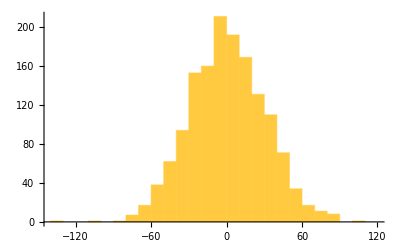
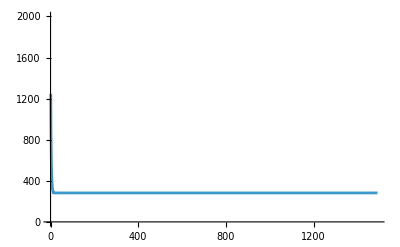
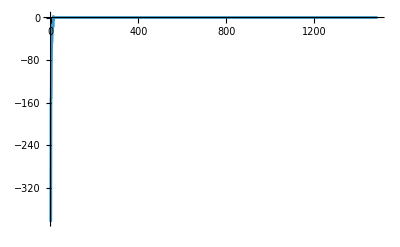
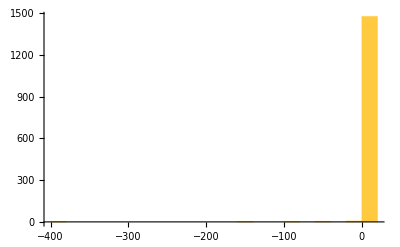
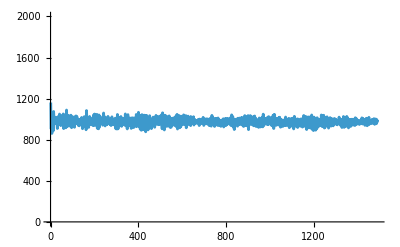
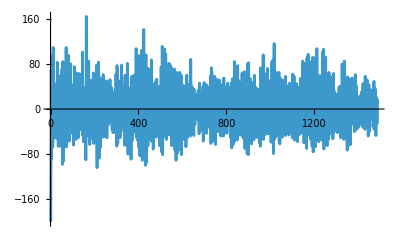
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[{ListLinePlot[Total/@#, PlotHighlighting->None, PlotRange->2000],ListLinePlot[Differences[Total/@ #], PlotHighlighting->None],Histogram[Differences[Total/@ #]],Rasterize[ArrayPlot[#]]}&[CellularAutomaton[{ResourceFunction["RandomCA"][{3, 1}]["RuleNumber"],3, 1},RandomInteger[2,1200],1490]], 20]
```

### Connecting it to chemical reaction networks?

### Connecting it to protein interaction networks?